```mathematica
<<"/home/denpak/Applications/Dynamica.m"
```

Dynamica (Version 1.0.11 - 5/8/2021), Copyright(c) 1993-2021 Randall D. Beer. All rights reserved.

THIS SOFTWARE IS DISTRIBUTED 'AS IS'. NO WARRANTY OF ANY KIND IS EXPRESSED OR IMPLIED.

```mathematica
gref=0.1
cap = 100
gpolt = 4.0
gpolh =0.01
epol = -70.0
gdep = 0.5 * gref
edep = 0.0
i = 0
gmin =0.2*gref
gmax=2.0*gref
vth =20.0
v0=2.0
gap = gmin + ((Gmax - gmin)/((1+Exp[(Vd-vth)/v0]) * (1+Exp[-(Vd+vth)/v0])))
```

0.1

100

4.

0.01

-70.

0.05

0.

0

0.02

0.2

20.

2.

0.02+(-0.02+Gmax)/((1+ⅇ^(0.5 (-20.-Vd))) (1+ⅇ^(0.5 (-20.+Vd))))

0.02+19.98/((1+ⅇ^(0.5 (-20.-Vd))) (1+ⅇ^(0.5 (-20.+Vd))))

0.02+(-0.02+Gmax)/((1+ⅇ^(0.5 (-20.+Vh-Vt))) (1+ⅇ^(0.5 (-20.-Vh+Vt))))

0.02+19.98/((1+ⅇ^(0.5 (-20.-vd))) (1+ⅇ^(0.5 (-20.+vd))))

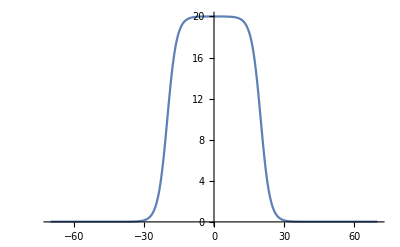

```mathematica
gapd = gap/.{Gmin->gmin,Gmax->20}
gaps = gap/.{Vd->Vh-Vt}
gapd/.Vd->vd
Plot[gapd/.Vd->vd,{vd,-70,70}]
```

```mathematica
ds = DynamicalSystem[{-gph*(Vh-epol)-gdep*(Vh-edep)-gaps*(Vh-Vt),-gpolt*(Vt-epol)-gdep*(Vt-edep)-gaps*(Vt-Vh)},{{Vh,-100,0},{Vt,-100,0}},{{gph,0,1},{Gmax,0,0.2}}]
eq = (-gph*(Vh-epol)-gdep*(Vh-edep)-gaps*(Vh-Vt)-(-gpolt*(Vt-epol)-gdep*(Vt-edep)-gaps*(Vt-Vh)))/.Vh->0
```

DynamicalSystem[«2 ODEs»,{Vh,Vt},{gph,Gmax}]

0.-70. gph+2 (0.02+(-0.02+Gmax)/((1+ⅇ^(0.5 (-20.-Vt))) (1+ⅇ^(0.5 (-20.+Vt))))) Vt+0.05 (0.+Vt)+4. (70.+Vt)

```mathematica
S= NSolve[eq==0,Vt]//FullSimplify
```

{}

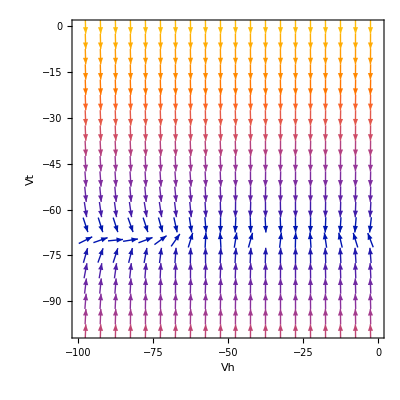

```mathematica
DisplayVectorField[ds/.gph->gpolh,VectorPoints->20]
```

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between t = 0. and t = 5.14776×10^-7.

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between t = 0. and t = 5.15081×10^-7.

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between t = 0. and t = 5.15385×10^-7.

General::stop: Further output of NDSolve::evcvmit will be suppressed during this calculation.

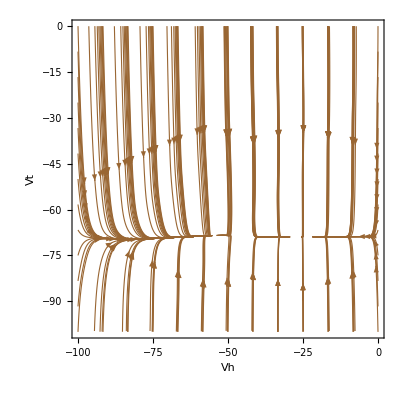

```mathematica
DisplayFlow[ds/.gph->gpolh,10]
```

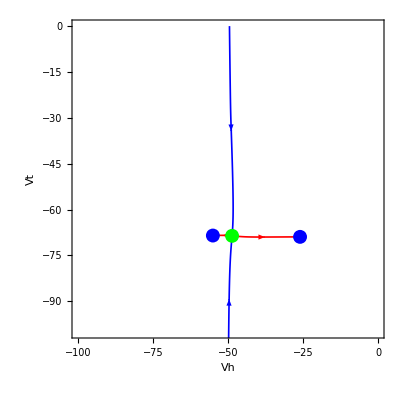

{EquilibriumPoint[Stable,Node,{-55.0394,-68.4932}],EquilibriumPoint[Saddle,Node,{-48.6428,-68.588}],EquilibriumPoint[Stable,Node,{-25.9819,-68.9237}]}

```mathematica
DisplayPhasePortrait[ds/.{Gmax->0.2,gph->0.01},SaddleManifolds->True]
$PhasePortraitEPs
```

```mathematica
DisplayBifurcationDiagram[ds,gph]
```

Too many free parameters for EquilibriumBranches: {Gmax,gph}

-Graphics-

```mathematica
Manipulate[Manipulate[DisplayPhasePortrait[ds/.{gph->gp,Gmax->gm},SaddleManifolds->True],{gm,1.5,0.2}],{gp,0,0.1}]
$Saddle
```

$Saddle

```mathematica
.
```

```mathematica
Point[EPEigenvectors[$PhasePortraitEPs[[2]]][[1]] + LSPoint[saddle]]
```

Point[{-48.5469,-67.5926}]

```mathematica
RegionPlot[{-48.54687063797946,-67.59262200313519}]
```

RegionPlot::argr: RegionPlot called with 1 argument; 3 arguments are expected.

RegionPlot[{-48.5469,-67.5926}]

```mathematica
saddle = $PhasePortraitEPs[[2]]
```

EquilibriumPoint[Saddle,Node,{-48.6428,-68.588}]

```mathematica
LSPoint[saddle]+
```

{-48.6428,-68.588}

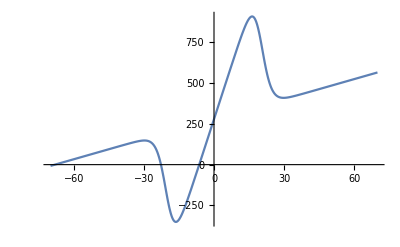

```mathematica
Plot[eq/.{gph->0.02,Gmax->20},{Vt,-70,70}]
```

```mathematica
Manipulate[Plot[eq/.{gph->gp,Gmax->gm},{Vt,-70,50}],{gp,0,2},{gm,0,20}]
```

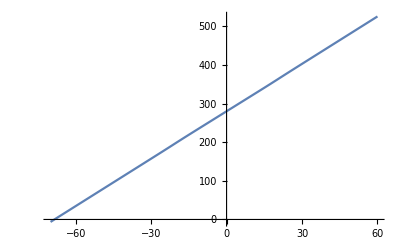
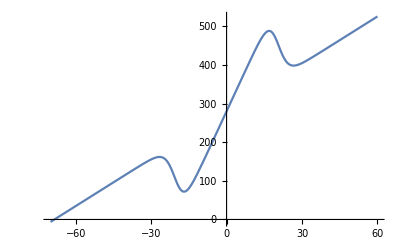
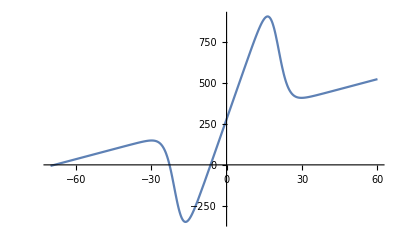
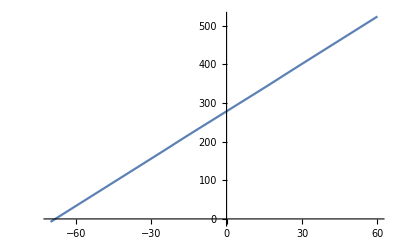
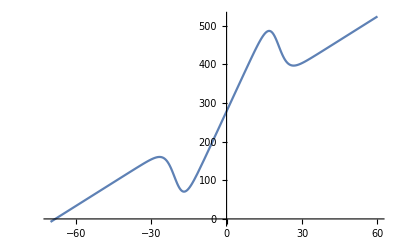
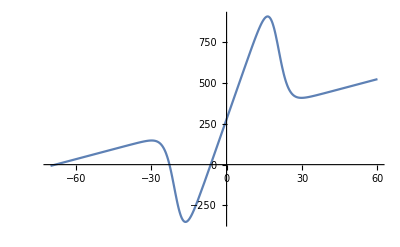
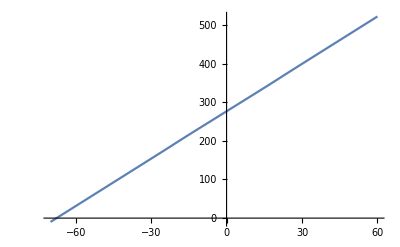
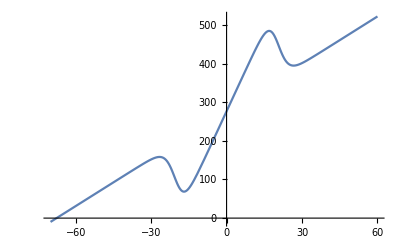

-Graphics-Gap PolarizationMaximum Gap Polarity

```mathematica
plots=Table[Plot[eq,{Vt,-70,60}],{gph,{0,0.02,0.05}},{Gmax,{0,5,20}}]
imgs=Transpose@plots;
Graphics[MapIndexed[Inset[Rasterize@#,#2]&,imgs,{2}],PlotRange->Thread[{1/4,2/3+Dimensions@imgs}],Axes->True,Ticks->Range@Dimensions@imgs,AxesStyle->Arrowheads[0.03],AxesOrigin->{1/4,1/4},ImageSize->700];
Labeled[%,{"Gap Polarization","Maximum Gap Polarity"},{Left,Bottom},RotateLabel->True]
```